```mathematica
nc:=0.01
γc:=1
γh:=1
f=0.1
ℏ:=1
κ=1/37
g:=14 *κ
ncav:=0.01
Δ1=0
Δ2=0
nh=4
```

0.1

1/37

0

0

4

```mathematica
n[1]
```

-0.505206+0. ⅈ

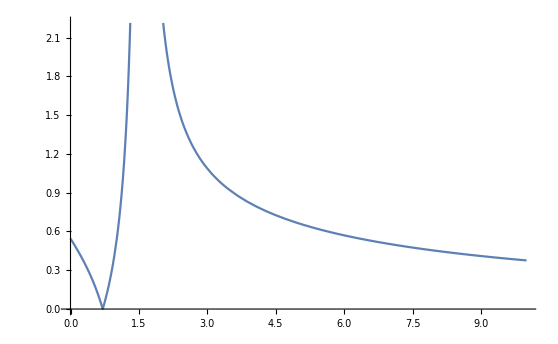

```mathematica
Plot[Abs[Re[n[nh]]],{nh,0,10}]
```

```mathematica
Solve[I (g σ21+Δ1 a†+f)−κ a†==0&&−I (g σ12+Δ1 a+f)−κ a&&(−I) g (σ21a−σ12a†)+γc ((nc+1) (1-p2-p1)−nc p2)==0&&−I g (σ12a†−σ21a)+γh ((nh+1) (1-p2-p1)−nh p1)==0&&−I (g (p2−(p2−p1) n)+f σ21+Δ1 σ21a−Δ2 σ21a)−γh 0.5 nh σ21a−γc  nc σ21a−κ σ21a==0&&−I (g (−p2−(p1−p2) n)-f σ12-Δ1 σ12a†+Δ2 σ12a†)−γh 0.5  nh σ12a†−γc 0.5  nc σ12a†−κ σ12a†==0&&−I g ((p1 −p2) a†)−γc 0.5 nc σ12−γh 0.5  nh σ12==0&&−I g ((p2 −p1) a)−γc 0.5 nc σ21−γh 0.5  nh σ21==0&&−I (g (σ12a†−σ21a)+f (a†−a))+2 κ (ncav−n)==0,{n,σ21a,σ12a†,σ12,σ21,p1,p2,a,a†}]
```

Solve::naqs: -a† κ+ⅈ (f+a† Δ1+g σ21)==0&&-a κ-ⅈ (f+a Δ1+g σ12)&&((1+nc) (1+Times[«2»]+Times[«2»])-nc p2) γc-ⅈ g (-σ12a†+σ21a)==0&&(-nh p1+(1+nh) (1+Times[«2»]+Times[«2»])) γh-ⅈ g (σ12a†-σ21a)==0&&-nc γc σ21a-0.5 nh γh σ21a-κ σ21a-ⅈ (g (p2+Times[«3»])+f σ21+Δ1 σ21a-Δ2 σ21a)==0&&-0.5 nc γc σ12a†-0.5 nh γh σ12a†-κ σ12a†-ⅈ (g (Times[«3»]+Times[«2»])-f σ12-Δ1 σ12a†+Δ2 σ12a†)==0&&-ⅈ a† g (p1-p2)-0.5 nc γc σ12-0.5 nh γh σ12==0&&-ⅈ a g (-p1+p2)-0.5 nc γc σ21-0.5 nh γh σ21==0&&2 (-n+ncav) κ-ⅈ ((Times[«2»]+a†) f+g (σ12a†+Times[«2»]))==0 is not a quantified system of equations and inequalities.

Solve[-a† κ+ⅈ (f+a† Δ1+g σ21)==0&&-a κ-ⅈ (f+a Δ1+g σ12)&&((1+nc) (1-p1-p2)-nc p2) γc-ⅈ g (-σ12a†+σ21a)==0&&(-nh p1+(1+nh) (1-p1-p2)) γh-ⅈ g (σ12a†-σ21a)==0&&-nc γc σ21a-0.5 nh γh σ21a-κ σ21a-ⅈ (g (p2-n (-p1+p2))+f σ21+Δ1 σ21a-Δ2 σ21a)==0&&-0.5 nc γc σ12a†-0.5 nh γh σ12a†-κ σ12a†-ⅈ (g (-n (p1-p2)-p2)-f σ12-Δ1 σ12a†+Δ2 σ12a†)==0&&-ⅈ a† g (p1-p2)-0.5 nc γc σ12-0.5 nh γh σ12==0&&-ⅈ a g (-p1+p2)-0.5 nc γc σ21-0.5 nh γh σ21==0&&2 (-n+ncav) κ-ⅈ ((-a+a†) f+g (σ12a†-σ21a))==0,{n,σ21a,σ12a†,σ12,σ21,p1,p2,a,a†}]

```mathematica
4.5
```

```mathematica
0.5*5
```

2.5